## Prep

```mathematica
Eq1=-(k12+k15) P1+P2*k21+P5*k51;
Eq2=-(k21+k23) P2+P3*k32+P1*k12;
Eq3=-(k32+k34) P3+P2*k23+P4*k43;
Eq4=-(k43+k45) P4+P3*k34+P5*k54;
Eq5=-(k54+k51) P5+P1*k15+P4*k45;
```

```mathematica
Pvec=Solve[{Eq1==0,Eq2==0,Eq3==0,Eq4==0,P1+P2+P3+P4+P5==1},{P1,P2,P3,P4,P5}];
```

```mathematica
Pvec[[1,5]]
```

P5→-((-k15 k21 k32 k43-k15 k21 k32 k45-k15 k21 k34 k45-k12 k23 k34 k45-k15 k23 k34 k45)/(k15 k21 k32 k43+k15 k21 k32 k45+k15 k21 k34 k45+k12 k23 k34 k45+k15 k23 k34 k45+k12 k23 k34 k51+k12 k23 k43 k51+k12 k32 k43 k51+k21 k32 k43 k51+k12 k23 k45 k51+k12 k32 k45 k51+k21 k32 k45 k51+k12 k34 k45 k51+k21 k34 k45 k51+k23 k34 k45 k51+k15 k21 k32 k54+k15 k21 k34 k54+k12 k23 k34 k54+k15 k23 k34 k54+k15 k21 k43 k54+k12 k23 k43 k54+k15 k23 k43 k54+k12 k32 k43 k54+k15 k32 k43 k54+k21 k32 k43 k54))

```mathematica
P1=-((-k21 k32 k43 k51-k21 k32 k45 k51-k21 k34 k45 k51-k23 k34 k45 k51-k21 k32 k43 k54)/(k15 k21 k32 k43+k15 k21 k32 k45+k15 k21 k34 k45+k12 k23 k34 k45+k15 k23 k34 k45+k12 k23 k34 k51+k12 k23 k43 k51+k12 k32 k43 k51+k21 k32 k43 k51+k12 k23 k45 k51+k12 k32 k45 k51+k21 k32 k45 k51+k12 k34 k45 k51+k21 k34 k45 k51+k23 k34 k45 k51+k15 k21 k32 k54+k15 k21 k34 k54+k12 k23 k34 k54+k15 k23 k34 k54+k15 k21 k43 k54+k12 k23 k43 k54+k15 k23 k43 k54+k12 k32 k43 k54+k15 k32 k43 k54+k21 k32 k43 k54));
P2=-((-k12 k32 k43 k51-k12 k32 k45 k51-k12 k34 k45 k51-k12 k32 k43 k54-k15 k32 k43 k54)/(k15 k21 k32 k43+k15 k21 k32 k45+k15 k21 k34 k45+k12 k23 k34 k45+k15 k23 k34 k45+k12 k23 k34 k51+k12 k23 k43 k51+k12 k32 k43 k51+k21 k32 k43 k51+k12 k23 k45 k51+k12 k32 k45 k51+k21 k32 k45 k51+k12 k34 k45 k51+k21 k34 k45 k51+k23 k34 k45 k51+k15 k21 k32 k54+k15 k21 k34 k54+k12 k23 k34 k54+k15 k23 k34 k54+k15 k21 k43 k54+k12 k23 k43 k54+k15 k23 k43 k54+k12 k32 k43 k54+k15 k32 k43 k54+k21 k32 k43 k54));
P3=-((-k12 k23 k43 k51-k12 k23 k45 k51-k15 k21 k43 k54-k12 k23 k43 k54-k15 k23 k43 k54)/(k15 k21 k32 k43+k15 k21 k32 k45+k15 k21 k34 k45+k12 k23 k34 k45+k15 k23 k34 k45+k12 k23 k34 k51+k12 k23 k43 k51+k12 k32 k43 k51+k21 k32 k43 k51+k12 k23 k45 k51+k12 k32 k45 k51+k21 k32 k45 k51+k12 k34 k45 k51+k21 k34 k45 k51+k23 k34 k45 k51+k15 k21 k32 k54+k15 k21 k34 k54+k12 k23 k34 k54+k15 k23 k34 k54+k15 k21 k43 k54+k12 k23 k43 k54+k15 k23 k43 k54+k12 k32 k43 k54+k15 k32 k43 k54+k21 k32 k43 k54));
P4=-((-k12 k23 k34 k51-k15 k21 k32 k54-k15 k21 k34 k54-k12 k23 k34 k54-k15 k23 k34 k54)/(k15 k21 k32 k43+k15 k21 k32 k45+k15 k21 k34 k45+k12 k23 k34 k45+k15 k23 k34 k45+k12 k23 k34 k51+k12 k23 k43 k51+k12 k32 k43 k51+k21 k32 k43 k51+k12 k23 k45 k51+k12 k32 k45 k51+k21 k32 k45 k51+k12 k34 k45 k51+k21 k34 k45 k51+k23 k34 k45 k51+k15 k21 k32 k54+k15 k21 k34 k54+k12 k23 k34 k54+k15 k23 k34 k54+k15 k21 k43 k54+k12 k23 k43 k54+k15 k23 k43 k54+k12 k32 k43 k54+k15 k32 k43 k54+k21 k32 k43 k54));
P5=-((-k15 k21 k32 k43-k15 k21 k32 k45-k15 k21 k34 k45-k12 k23 k34 k45-k15 k23 k34 k45)/(k15 k21 k32 k43+k15 k21 k32 k45+k15 k21 k34 k45+k12 k23 k34 k45+k15 k23 k34 k45+k12 k23 k34 k51+k12 k23 k43 k51+k12 k32 k43 k51+k21 k32 k43 k51+k12 k23 k45 k51+k12 k32 k45 k51+k21 k32 k45 k51+k12 k34 k45 k51+k21 k34 k45 k51+k23 k34 k45 k51+k15 k21 k32 k54+k15 k21 k34 k54+k12 k23 k34 k54+k15 k23 k34 k54+k15 k21 k43 k54+k12 k23 k43 k54+k15 k23 k43 k54+k12 k32 k43 k54+k15 k32 k43 k54+k21 k32 k43 k54));
```

```mathematica
P5*k51-P1*k15
```

-(((-k15 k21 k32 k43-k15 k21 k32 k45-k15 k21 k34 k45-k12 k23 k34 k45-k15 k23 k34 k45) k51)/(k15 k21 k32 k43+k15 k21 k32 k45+k15 k21 k34 k45+k12 k23 k34 k45+k15 k23 k34 k45+k12 k23 k34 k51+k12 k23 k43 k51+k12 k32 k43 k51+k21 k32 k43 k51+k12 k23 k45 k51+k12 k32 k45 k51+k21 k32 k45 k51+k12 k34 k45 k51+k21 k34 k45 k51+k23 k34 k45 k51+k15 k21 k32 k54+k15 k21 k34 k54+k12 k23 k34 k54+k15 k23 k34 k54+k15 k21 k43 k54+k12 k23 k43 k54+k15 k23 k43 k54+k12 k32 k43 k54+k15 k32 k43 k54+k21 k32 k43 k54))+(k15 (-k21 k32 k43 k51-k21 k32 k45 k51-k21 k34 k45 k51-k23 k34 k45 k51-k21 k32 k43 k54))/(k15 k21 k32 k43+k15 k21 k32 k45+k15 k21 k34 k45+k12 k23 k34 k45+k15 k23 k34 k45+k12 k23 k34 k51+k12 k23 k43 k51+k12 k32 k43 k51+k21 k32 k43 k51+k12 k23 k45 k51+k12 k32 k45 k51+k21 k32 k45 k51+k12 k34 k45 k51+k21 k34 k45 k51+k23 k34 k45 k51+k15 k21 k32 k54+k15 k21 k34 k54+k12 k23 k34 k54+k15 k23 k34 k54+k15 k21 k43 k54+k12 k23 k43 k54+k15 k23 k43 k54+k12 k32 k43 k54+k15 k32 k43 k54+k21 k32 k43 k54)

## Eqs

```mathematica
jmec[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=(k12 k23 k34 k45 k51-k15 k21 k32 k43 k54)/((k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45) k51+k21 k32 k43 k54+k15 (k23 k34 k45+k32 k43 k54+k23 (k34+k43) k54+k21 (k34 k45+(k34+k43) k54+k32 (k43+k45+k54)))+k12 (k34 k45 k51+k32 (k43+k45) k51+k32 k43 k54+k23 ((k43+k45) k51+k43 k54+k34 (k45+k51+k54))))
```

```mathematica
jmecp[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=(k12 k23 k34 k45 k51)/((k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45) k51+k21 k32 k43 k54+k15 (k23 k34 k45+k32 k43 k54+k23 (k34+k43) k54+k21 (k34 k45+(k34+k43) k54+k32 (k43+k45+k54)))+k12 (k34 k45 k51+k32 (k43+k45) k51+k32 k43 k54+k23 ((k43+k45) k51+k43 k54+k34 (k45+k51+k54))))
```

```mathematica
jmecn[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=(k15 k21 k32 k43 k54)/((k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45) k51+k21 k32 k43 k54+k15 (k23 k34 k45+k32 k43 k54+k23 (k34+k43) k54+k21 (k34 k45+(k34+k43) k54+k32 (k43+k45+k54)))+k12 (k34 k45 k51+k32 (k43+k45) k51+k32 k43 k54+k23 ((k43+k45) k51+k43 k54+k34 (k45+k51+k54))))
```

```mathematica
k12[T_,k12o_,kai12_,f_,d_,beta_]:=2*k12o/(1+Exp[kai12*f*d*beta])
k21[D_,k21o_,kai12_,f_,d_,beta_]:=D*2*k21o/(1+Exp[kai12*f*d*beta])
k23[k23o_,kai23_,f_,d_,beta_]:=2*k23o/(1+Exp[kai23*f*d*beta])
k32[k32o_,kai23_,f_,d_,beta_]:=2*k32o/(1+Exp[kai23*f*d*beta])
k34[k34o_,kai34_,f_,d_,beta_]:=2*k34o/(1+Exp[kai34*f*d*beta])
k43[P_,k43o_,kai34_,f_,d_,beta_]:=P*2*k43o/(1+Exp[kai34*f*d*beta])
k45[T_,k45o_,kai45_,f_,d_,beta_]:=2*T*k45o/(1+Exp[kai45*f*d*beta])
k54[k54o_,kai45_,f_,d_,beta_]:=2*k54o/(1+Exp[kai45*f*d*beta])
k51[k51o_,theta_,f_,d_,beta_]:=k51o*Exp[-beta*f*d*theta]
k15[T_,k15o_,theta_,f_,d_,beta_]:=k15o*Exp[beta*f*d*(1-theta)]
```

```mathematica
jmecFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=jmec[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
jmecpFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=jmecp[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
jmecnFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=jmecn[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

## Data

```mathematica
data1={{-2.266,1011.490},{-1.257,986.226},{1.044,685.203},{2.095,555.649},{2.999,343.655},{3.657,183.621},{3.988,113.454},{4.531,43.512},{4.994,39.543},{5.28,-48.319},{6.119,-37.334},{7.066,-53.842},{7.991,-55.274},{8.990,-62.005}};



data2={{-4.019,250.851},{-2.028,275.664},{-1.019,252.701},{1.004,235.793},{1.999,196.908},{2.992,150.968},{3.984,78.861},{4.984,32.529},{5.979,1.537},{6.994,-11.004},{7.996,-18.028},{8.972,-28.255}};
```

## MSD

```mathematica
MSE2[k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=Sum[((data1[[i,2]]-d*jmecFT[data1[[i,1]],1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta])/data1[[1,2]])^2,{i,9}]+Sum[((data2[[i,2]]-d*jmecFT[data2[[i,1]],10,1,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta])/data2[[1,2]])^2,{i,9}]
```

## Fit

```mathematica
FindMinimum[{MSE2[k12o,k23o,k34o,k45o,3*10^5,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,8,1/4.114],k12o>0,k23o>0,k34o>0,k45o>0,k21o>0,k32o>0,k43o>0,k54o>0,k15o>0,kai12>0,kai23>0,kai34>0,kai45>0,1>theta>0},{k12o,k23o,k34o,k45o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta}]
```

{0.0174513,{k12o→391.049,k23o→355.261,k34o→450.056,k45o→32.169,k21o→1.48004,k32o→15.5334,k43o→2.97732,k54o→95.0347,k15o→0.593955,kai12→0.446158,kai23→0.00318925,kai34→0.000245267,kai45→0.00477035,theta→0.999989}}

```mathematica
param3={k12o->384.4,k23o->371.2,k34o->459.5,k45o->29.8,k51o->3*10^5,k21o->1.5,k32o->33.2,k43o->2.7,k54o->94.7,k15o->0.7,kai12->0.4,kai23->0,kai34->0,kai45->0,theta->1,d->8,beta->1/4.114};
```

## Q

```mathematica
Qchem[k12_,k23_,k34_,k45_,k21_,k32_,k43_,k54_]:=Log[(k12*k23*k34*k45)/(k21*k32*k43*k54)]
```

```mathematica
Qmec[k51_,k15_]:=Log[k51/k15]
```

```mathematica
Q[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=Qchem[k12,k23,k34,k45,k21,k32,k43,k54]+Qmec[k51,k15]
```

```mathematica
Qx[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=Log[(k12*k45)/(k21*k54)]
```

```mathematica
Qy[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=Log[(k23*k34)/(k32*k43)]
```

```mathematica
QchemFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=Qchem[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta]]
```

```mathematica
QmecFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=Qmec[k51[k51o,theta,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
QFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=Q[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
QxFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=Qx[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
QyFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=Qy[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

## Rho

```mathematica
FullSimplify[k51*P5/(k15*P1)]
```

((k12 k23 k34 k45+k15 (k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45)) k51)/(k15 (k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45) k51+k15 k21 k32 k43 k54)

```mathematica
rhox[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=Log[(k12 k45 (k15 (k23 k34+k21 (k32+k34)) k54+k12 k23 k34 (k51+k54)) (k23 k34 k45 k51+k21 (k34 k45 k51+k32 (k43+k45) k51+k32 k43 k54)))/(k21 (k12 k23 k34 k45+k15 (k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45)) k54 (k12 (k34 k45+k32 (k43+k45)) k51+(k12+k15) k32 k43 k54))]
```

```mathematica
rhoy[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=Log[(k23 k34 (k12 (k34 k45+k32 (k43+k45)) k51+(k12+k15) k32 k43 k54))/(k32 k43 (k15 (k23 k34+k21 (k32+k34)) k54+k12 k23 k34 (k51+k54)))]
```

```mathematica
rhomec[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=Log[((k12 k23 k34 k45+k15 (k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45)) k51)/(k15 (k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45) k51+k15 k21 k32 k43 k54)]
```

```mathematica
rho[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=rhox[k12,k23,k34,k45,k51,k21,k32,k43,k54,k15]+rhoy[k12,k23,k34,k45,k51,k21,k32,k43,k54,k15]
```

```mathematica
rhoyFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=rhoy[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
rhoxFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=rhox[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
rhoFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=rho[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
rhomecFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=rhomec[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

## I

```mathematica
FullSimplify[P2/P4]
```

(k12 (k34 k45+k32 (k43+k45)) k51+(k12+k15) k32 k43 k54)/(k15 (k23 k34+k21 (k32+k34)) k54+k12 k23 k34 (k51+k54))

```mathematica
Ix[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=Log[(k12 (k34 k45+k32 (k43+k45)) k51+(k12+k15) k32 k43 k54)/(k15 (k23 k34+k21 (k32+k34)) k54+k12 k23 k34 (k51+k54))]
```

```mathematica
Ix2cycle[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=Log[((k12 k23 k34 k45+k15 (k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45)) (k12 (k34 k45+k32 (k43+k45)) k51+(k12+k15) k32 k43 k54) ((k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45) k51+k21 k32 k43 k54+k12 k23 k34 (k45+k51+k54)+k15 (k21 k34 (k45+k54)+k23 k34 (k45+k54)+k21 k32 (k43+k45+k54))))/((k15 (k23 k34+k21 (k32+k34)) k54+k12 k23 k34 (k51+k54)) ((k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45) k51+k21 k32 k43 k54+k15 (k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45+k32 k43 k54)+k12 (k23 k34 k45+k32 k43 k51+(k32+k34) k45 k51+k32 k43 k54)) (k23 k34 k45 k51+k21 (k34 k45 k51+k32 (k43+k45) k51+k32 k43 k54)))]
```

```mathematica
Iy2cycle[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=Log[((k15 (k23 k34+k21 (k32+k34)) k54+k12 k23 k34 (k51+k54)) ((k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45) k51+k21 k32 k43 k54+k15 (k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45+k32 k43 k54)+k12 (k23 k34 k45+k32 k43 k51+(k32+k34) k45 k51+k32 k43 k54)))/((k12 (k34 k45+k32 (k43+k45)) k51+(k12+k15) k32 k43 k54) ((k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45) k51+k21 k32 k43 k54+k12 k23 k34 (k45+k51+k54)+k15 (k21 k34 (k45+k54)+k23 k34 (k45+k54)+k21 k32 (k43+k45+k54))))]
```

```mathematica
Iy[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=Log[((((k12+k21) k32 k43+(k12+k21) k32 k45+(k12+k21+k23) k34 k45) k51+(k12+k15+k21) k32 k43 k54) (k15 (k23 k34+k21 (k32+k34)) k54+k12 k23 k34 (k51+k54)))/((k12 (k34 k45+k32 (k43+k45)) k51+(k12+k15) k32 k43 k54) (k12 k23 k34 (k45+k51+k54)+k15 (k21 k34 (k45+k54)+k23 k34 (k45+k54)+k21 k32 (k43+k45+k54))))]
```

```mathematica
FullSimplify[P5/P1]
```

(k12 k23 k34 k45+k15 (k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45))/(k23 k34 k45 k51+k21 (k34 k45 k51+k32 (k43+k45) k51+k32 k43 k54))

```mathematica
I2cycle[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=Log[(k12 k23 k34 k45+k15 (k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45))/(k23 k34 k45 k51+k21 (k34 k45 k51+k32 (k43+k45) k51+k32 k43 k54))]
```

```mathematica
DelI[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=Ix[k12,k23,k34,k45,k51,k21,k32,k43,k54,k15]+Iy[k12,k23,k34,k45,k51,k21,k32,k43,k54,k15]
```

```mathematica
IxFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=Ix[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
IyFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=Iy[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
IFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=DelI[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
Ix2cycleFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=Ix2cycle[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
Iy2cycleFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=Iy2cycle[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
I2cycleFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=I2cycle[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

## S

```mathematica
FullSimplify[P5/P1]
```

(k12 k23 k34 k45+k15 (k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45))/(k23 k34 k45 k51+k21 (k34 k45 k51+k32 (k43+k45) k51+k32 k43 k54))

```mathematica
DelSx[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=Log[(k23 k34 k45 k51+k21 (k34 k45 k51+k32 (k43+k45) k51+k32 k43 k54))/(k12 k23 k34 k45+k15 (k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45))]
```

```mathematica
DelSy[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=Log[(((k12+k21) k32 k43+(k12+k21) k32 k45+(k12+k21+k23) k34 k45) k51+(k12+k15+k21) k32 k43 k54)/(k12 k23 k34 (k45+k51+k54)+k15 (k21 k34 (k45+k54)+k23 k34 (k45+k54)+k21 k32 (k43+k45+k54)))]
```

```mathematica
DelSxy[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=Log[(k23 k34 k45 k51+k21 (k34 k45 k51+k32 (k43+k45) k51+k32 k43 k54))/(k12 k23 k34 k45+k15 (k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45))]
```

```mathematica
DelSxymc[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=Log[(k12 k23 k34 k45+k15 (k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45))/(k23 k34 k45 k51+k21 (k34 k45 k51+k32 (k43+k45) k51+k32 k43 k54))]
```

```mathematica
DelS[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=DelSx[k12,k23,k34,k45,k51,k21,k32,k43,k54,k15]+DelSy[k12,k23,k34,k45,k51,k21,k32,k43,k54,k15]
```

```mathematica
DelSxFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=DelSx[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
DelSyFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=DelSy[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
DelSFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=DelS[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
DelSxyFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=DelSxy[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
DelSxymcFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=DelSxymc[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

## μ

```mathematica
μchemFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=DelSxyFT[f,T,D,P,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]+QchemFT[f,T,D,P,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]
```

```mathematica
μmecFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=-DelSxyFT[f,T,D,P,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]+QmecFT[f,T,D,P,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]+f*d*beta
```

## Sigma

```mathematica
σchemFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=DelSFT[f,T,D,P,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]+QchemFT[f,T,D,P,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]
```

```mathematica
σchemxFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=DelSxFT[f,T,D,P,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]+QxFT[f,T,D,P,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]
```

```mathematica
σchemyFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=DelSyFT[f,T,D,P,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]+QyFT[f,T,D,P,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]
```

## Jmec

```mathematica
FullSimplify[k15*P1]
```

(k15 (k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45) k51+k15 k21 k32 k43 k54)/((k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45) k51+k21 k32 k43 k54+k15 (k23 k34 k45+k32 k43 k54+k23 (k34+k43) k54+k21 (k34 k45+(k34+k43) k54+k32 (k43+k45+k54)))+k12 (k34 k45 k51+k32 (k43+k45) k51+k32 k43 k54+k23 ((k43+k45) k51+k43 k54+k34 (k45+k51+k54))))

```mathematica
A[k12_,k23_,k34_,k45_,k51_,k21_,k32_,k43_,k54_,k15_]:=(k15 (k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45) k51+k15 k21 k32 k43 k54)/((k21 k32 k43+k23 k34 k45+k21 (k32+k34) k45) k51+k21 k32 k43 k54+k15 (k23 k34 k45+k32 k43 k54+k23 (k34+k43) k54+k21 (k34 k45+(k34+k43) k54+k32 (k43+k45+k54)))+k12 (k34 k45 k51+k32 (k43+k45) k51+k32 k43 k54+k23 ((k43+k45) k51+k43 k54+k34 (k45+k51+k54))))
```

```mathematica
AFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=A[k12[T,k12o,kai12,f,d,beta],k23[k23o,kai23,f,d,beta],k34[k34o,kai34,f,d,beta],k45[T,k45o,kai45,f,d,beta],k51[k51o,theta,f,d,beta],k21[D,k21o,kai12,f,d,beta],k32[k32o,kai23,f,d,beta],k43[P,k43o,kai34,f,d,beta],k54[k54o,kai45,f,d,beta],k15[T,k15o,theta,f,d,beta]]
```

```mathematica
JmecFT[f_,T_,D_,P_,k12o_,k23o_,k34o_,k45o_,k51o_,k21o_,k32o_,k43o_,k54o_,k15o_,kai12_,kai23_,kai34_,kai45_,theta_,d_,beta_]:=AFT[f,T,D,P,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]*(Exp[μmecFT[f,T,D,P,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]-f*d*beta]-1)
```

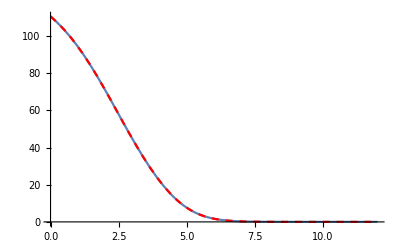

```mathematica
Show[Plot[JmecFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,0,12}],Plot[jmecFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,0,12},PlotStyle->{Dashed,Red}],PlotRange->All]
```

## Graphs

## Prep

```mathematica
nb1=NotebookOpen["/Users/Ryota/Box\ Sync/Thi\ lab/kinesin/ATP/Minimal\ model/ListOfSymbols.nb"];
SelectionMove[nb1,All,Notebook]
SelectionEvaluate[nb1]
```

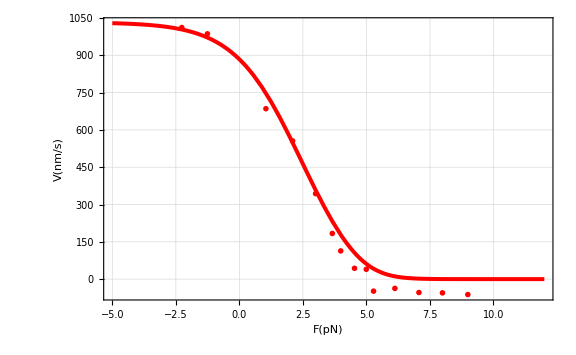

```mathematica
fit1=Show[Plot[d*jmecFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-5,12},PlotStyle->{Thickness[0.005],Red}],ListPlot[data1,PlotMarkers->{{myFilledCircle/.myColor->Red,0.04}}],ImageSize->Large,Frame->True,Axes->False,FrameLabel->{{"V(nm/s)",""},{"F(pN)",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],PlotRange->All,GridLines->Automatic]
```

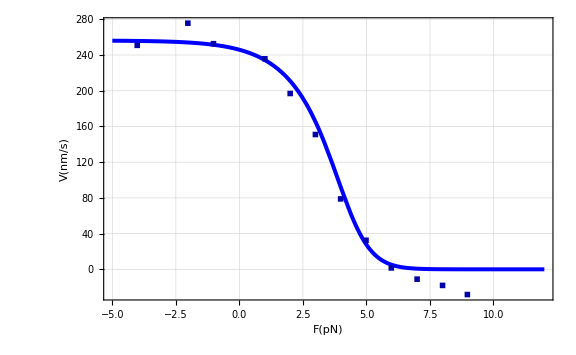

```mathematica
fit2=Show[Plot[d*jmecFT[f,10,1,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-5,12},PlotStyle->{Thickness[0.005],Blue}],ListPlot[data2,PlotMarkers->{{myFilledSquare/.myColor->Darker[Blue],0.04}}],ImageSize->Large,Frame->True,Axes->False,FrameLabel->{{"V(nm/s)",""},{"F(pN)",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],PlotRange->All,GridLines->Automatic]
```

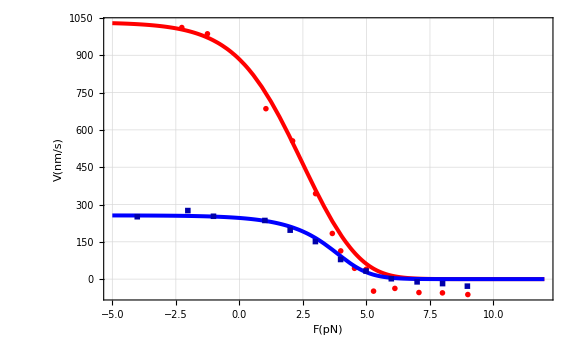

```mathematica
Show[fit1,fit2]
```

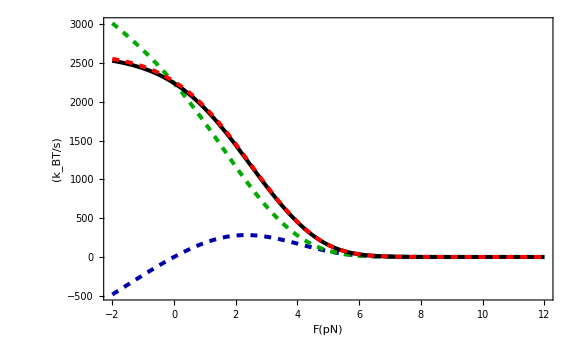

```mathematica
figmu1=Show[Plot[(f*d*beta)*jmecFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Thickness[0.005],Darker[Blue],Dashed}],Plot[(QFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta])*jmecFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Thickness[0.005],Darker[Green],Dashed }],Plot[(f*d*beta+QFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta])*jmecFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Thickness[0.005],Black}],{Plot[jmecFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]*20.5/.param3,{f,-2,12},PlotStyle->{Dashed,Red,Thickness[0.005]}]},ImageSize->Large,Frame->True,Axes->False,FrameLabel->{{"(k_BT/s)",""},{"F(pN)",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],PlotRange->All]
```

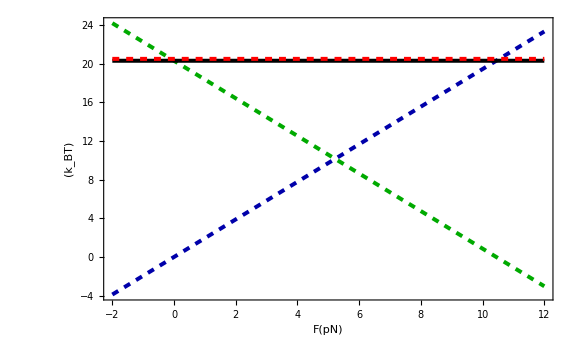

```mathematica
Show[Plot[(f*d*beta)/.param3,{f,-2,12},PlotStyle->{Thickness[0.005],Darker[Blue],Dashed}],Plot[(QFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta])/.param3,{f,-2,12},PlotStyle->{Thickness[0.005],Darker[Green],Dashed }],Plot[(f*d*beta+QFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta])/.param3,{f,-2,12},PlotStyle->{Thickness[0.005],Black}],{Plot[20.5/.param3,{f,-2,12},PlotStyle->{Dashed,Red,Thickness[0.005]}]},ImageSize->Large,Frame->True,Axes->False,FrameLabel->{{"(k_BT)",""},{"F(pN)",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],PlotRange->All]
```

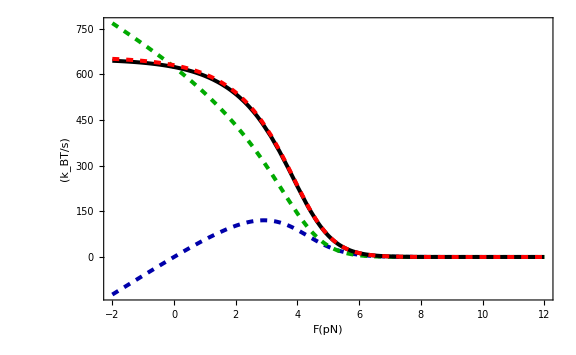

```mathematica
figmu2=Show[Plot[(f*d*beta)*jmecFT[f,10,1,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Thickness[0.005],Darker[Blue],Dashed}],Plot[(QFT[f,10,1,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta])*jmecFT[f,10,1,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Thickness[0.005],Darker[Green],Dashed }],Plot[(f*d*beta+QFT[f,10,1,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta])*jmecFT[f,10,1,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Thickness[0.005],Black}],{Plot[jmecFT[f,10,1,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]*20.5/.param3,{f,-2,12},PlotStyle->{Dashed,Red,Thickness[0.005]}]},ImageSize->Large,Frame->True,Axes->False,FrameLabel->{{"(k_BT/s)",""},{"F(pN)",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],PlotRange->All]
```

```mathematica
Show[Plot[(f*d*beta)/.param3,{f,-2,12},PlotStyle->{Thickness[0.005],Darker[Blue],Dashed}],Plot[(QFT[f,10,1,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta])/.param3,{f,-2,12},PlotStyle->{Thickness[0.005],Darker[Green],Dashed }],Plot[(f*d*beta+QFT[f,10,1,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta])/.param3,{f,-2,12},PlotStyle->{Thickness[0.005],Black}],{Plot[20.5/.param3,{f,-2,12},PlotStyle->{Dashed,Red,Thickness[0.005]}]},ImageSize->Large,Frame->True,Axes->False,FrameLabel->{{"(k_BT)",""},{"F(pN)",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],PlotRange->All]
```

-Graphics-

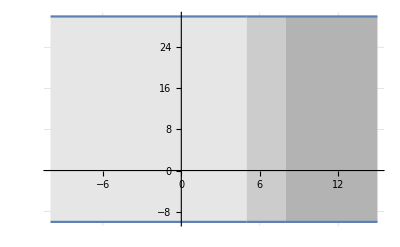

```mathematica
color=Show[Plot[30,{x,-10,5.0},Filling->Bottom,FillingStyle->{GrayLevel[0.9]}],Plot[30,{x,5.0,8},Filling->{Bottom},FillingStyle->{GrayLevel[0.8]}],Plot[30,{x,8,15},Filling->{Bottom},FillingStyle->{GrayLevel[0.7]}],Plot[-10,{x,-10,5.0},Filling->Top,FillingStyle->{GrayLevel[0.9]}],Plot[-10,{x,5.0,8},Filling->{Top},FillingStyle->{GrayLevel[0.8]}],Plot[-10,{x,8,15},Filling->{Top},FillingStyle->{GrayLevel[0.7]}],PlotRange->{-10,30},GridLines->Automatic]
```

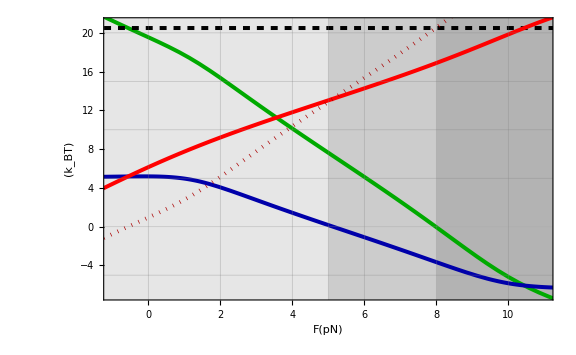

```mathematica
Show[color,Plot[σchemFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Darker[Green],Thickness[0.005]}],Plot[IFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Thickness[0.005],Darker[Blue]}],Plot[20.5/.param3,{f,-2,12},PlotStyle->{Dashed,Black,Thickness[0.005]}],Plot[IFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]+20.5-σchemFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Red,Thickness[0.005]}],Plot[20.5-σchemFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Darker[Red],Dotted,Thickness[0.005]}],PlotRange->{{-1,11},{-7,21}},ImageSize->Large,Frame->True,Axes->False,FrameLabel->{{"(k_BT)",""},{"F(pN)",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],GridLines->{{0,2,4,{5,{Thick,Darker[Black]}},6,{8,{Thick,Darker[Black]}},10},{-5,0,5,10,15,20}},Method->{"GridLinesInFront"->True}]
```

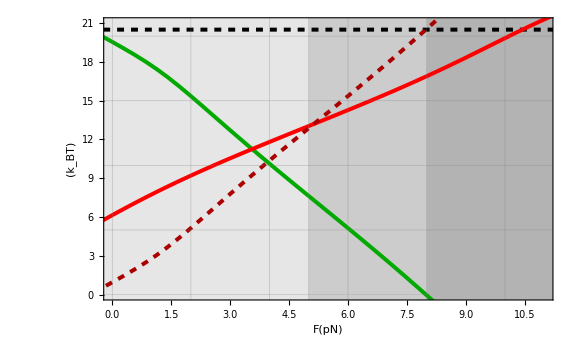

```mathematica
Show[color,Plot[σchemFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Darker[Green],Thickness[0.005]}],Plot[20.5/.param3,{f,-2,12},PlotStyle->{Dashed,Black,Thickness[0.005]}],Plot[IFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]+20.5-σchemFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Red,Thickness[0.005]}],Plot[20.5-σchemFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Darker[Red],Dashed,Thickness[0.005]}],PlotRange->{{0,11},{0,21}},ImageSize->Large,Frame->True,Axes->False,FrameLabel->{{"(k_BT)",""},{"F(pN)",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],GridLines->{{0,2,4,{5,{Thick,Darker[Black]}},6,{8,{Thick,Darker[Black]}},10},{-5,0,5,10,15,20}},Method->{"GridLinesInFront"->True}]
```

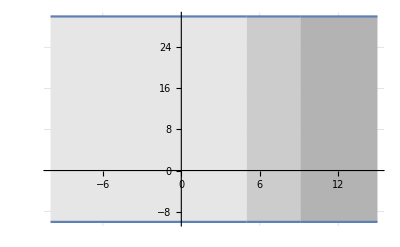

```mathematica
color2=Show[Plot[30,{x,-10,5},Filling->Bottom,FillingStyle->{GrayLevel[0.9]}],Plot[30,{x,5,9.1},Filling->{Bottom},FillingStyle->{GrayLevel[0.8]}],Plot[30,{x,9.1,15},Filling->{Bottom},FillingStyle->{GrayLevel[0.7]}],Plot[-10,{x,-10,5},Filling->Top,FillingStyle->{GrayLevel[0.9]}],Plot[-10,{x,5,9.1},Filling->{Top},FillingStyle->{GrayLevel[0.8]}],Plot[-10,{x,9.1,15},Filling->{Top},FillingStyle->{GrayLevel[0.7]}],PlotRange->{-10,30},GridLines->Automatic,Method->{"GridLinesInFront"->True}]
```

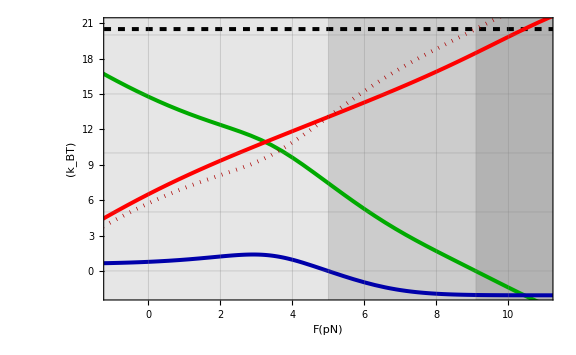

```mathematica
Show[color2,Plot[σchemFT[f,10,1,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Darker[Green],Thickness[0.005]}],Plot[IFT[f,10,1,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Thickness[0.005],Darker[Blue]}],Plot[20.5/.param3,{f,-2,12},PlotStyle->{Dashed,Black,Thickness[0.005]}],Plot[IFT[f,10,1,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]+20.5-σchemFT[f,10,1,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Red,Thickness[0.005]}],Plot[20.5-σchemFT[f,10,1,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Darker[Red],Dotted,Thickness[0.005]}],PlotRange->{{-1,11},{-2,21}},ImageSize->Large,Frame->True,Axes->False,FrameLabel->{{"(k_BT)",""},{"F(pN)",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],GridLines->{{0,2,4,{5,{Thick,Darker[Black]}},6,8,{9.1,{Thick,Darker[Black]}},10},{0,5,10,15,20}},Method->{"GridLinesInFront"->True}]
```

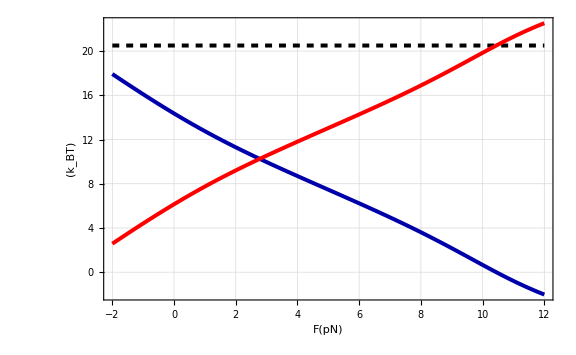

```mathematica
s1=Show[Plot[20.5,{f,-2,12},PlotStyle->{Black,Dashed,Thickness[0.005]}],Plot[-IFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]+σchemFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Darker[Blue],Thickness[0.005]}],Plot[IFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]+20.5-σchemFT[f,1000,100,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,-2,12},PlotStyle->{Red,Thickness[0.005]}],PlotRange->All,ImageSize->Large,Frame->True,Axes->False,FrameLabel->{{"(k_BT)",""},{"F(pN)",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],GridLines->Automatic]
```

### Find zeros for delta i

```mathematica
T=1000;DD=100;
FindRoot[IFT[f,T,DD,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,5}]
```

{f→5.13276}

```mathematica
T=500;DD=100;
FindRoot[IFT[f,T,DD,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,5}]
```

{f→5.13196}

```mathematica
T=100;DD=100;
FindRoot[IFT[f,T,DD,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,5}]
```

{f→5.12554}

```mathematica
T=50;DD=100;
FindRoot[IFT[f,T,DD,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,5}]
```

{f→5.11757}

```mathematica
T=10;DD=100;
FindRoot[IFT[f,T,DD,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,5}]
```

{f→5.05559}

```mathematica
listT100={{1000,5.132763149914706},{500,5.1319588072806495},{100,5.125543603895712},{50,5.117572731332829},{10,5.05559302549402}};
```

```mathematica
T=1000;DD=1;
FindRoot[IFT[f,T,DD,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,5}]
```

{f→5.1209}

```mathematica
T=500;DD=1;
FindRoot[IFT[f,T,DD,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,5}]
```

{f→5.11953}

```mathematica
T=100;DD=1;
FindRoot[IFT[f,T,DD,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,5}]
```

{f→5.10859}

```mathematica
T=50;DD=1;
FindRoot[IFT[f,T,DD,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,5}]
```

{f→5.09505}

```mathematica
T=10;DD=1;
FindRoot[IFT[f,T,DD,1000,k12o,k23o,k34o,k45o,k51o,k21o,k32o,k43o,k54o,k15o,kai12,kai23,kai34,kai45,theta,d,beta]/.param3,{f,5}]
```

{f→4.99104}

```mathematica
listT1={{1000,5.120902992660075},{500,5.119529528356622},{100,5.10859257538333},{50,5.095045218404206},{10,4.991041272707499}};
```

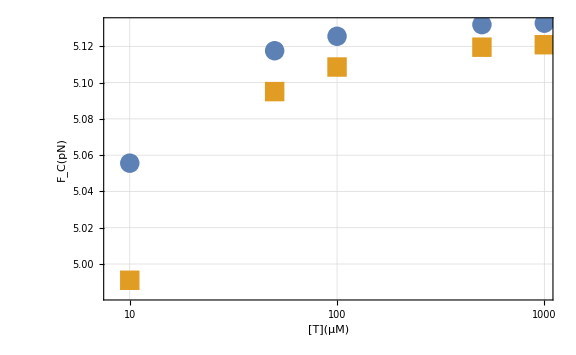

```mathematica
Show[ListLogLinearPlot[{listT100,listT1},PlotMarkers->{Automatic,20}],ImageSize->Large,Frame->True,Axes->False,FrameLabel->{{"F_C(pN)",""},{"[T](μM)",""}},LabelStyle->Directive[Black,20],FrameStyle->Directive[Black,20],TicksStyle->Directive[Black,20],GridLines->Automatic]
```